# Assignment 2

Course code: IX1500
Date: 20yy-mm-dd

Leo Karsikas, leoka@kth.se
Jonathan Johnson, jjohnso@kth.se

Task 1: RSA

## Summery

### Task

Ni ska använda RSA kryptering för att kryptera ovanstående citat (se 2.2.4 ovan), där n skall vara högst 200 bitar och e ett litet tal, ca 10^3-10^4 stort. Se 2.2.4 för hur dessa ska generas. Koda citatet enligt metoden i 2.2.4 (tal med basen 256). Observera att om meddelandet kodas till talet m så måste m < n. Om inte, så dela upp citatet på flera rader och kryptera varje rad för sig. Tips: Funktioner som kan behövas: FactorInteger, Partition.

Dekryptera sedan meddelandet och verifirera att ni får samma resultat som ursprunget.

Undersök sedan sambandet mellan nyckellängd (i bitar) och tid för att kryptera och dekryptera meddelanden. Rita en graf för sambandet mellan nyckelängd, n , och exekveringstid. Låt n variera upp till 2048 bitar. Tips: Funktion: Timing

### Solution

1. The first step in the solution is to decide p and q as two random large prime number between 2^99 and 2^100 to build n=p*q (since we want an n ~2^200)

2. Next we choose two numbers e and d, where e·d≡1 mod ℤ_(ϕ(n))
   We choose e as a relative prime to ϕ(n)=(p-1)(q-1) , this guarantees it has an inverse d in ℤ_(ϕ(n)).
   e is chosen as a relatively small number, in order to keep encryption efficient, we do this by simply testing random integers
   between 10^3 and 10^4 until we find one fulfilling gcd(e,ϕ(n))=1, then simply choose it’s inverse (in ℤ_(ϕ(n))) as d.
   e and n makes up the encryption key and is publicly “published” p, q and d are kept secret.
  
3. To encrypt the message M as a crypt C:
	C≡M^e mod n

4. To decrypt said crypt as D:
          D≡ C^d mod n

For this to be useful we need do know that
D = M

With simple substitution in the above algorithm we see that
D≡_n C^d≡_n(M^e)^d≡_n M^ed

and since e and d are inverses in ℤ_(ϕ(n)) and therefore e d≡1mod ℤ_(ϕ(n)) 
M^ed=M^(1+k(ϕ(n)))=M·(M^(ϕ(n)))^k

Eulers totient theorem shows that
M^(ϕ(n))≡ 1 mod n
⇒
M·(M^(ϕ(n)))^k≡_n M·1
⇒
D≡M mod n

And lastly, since we make sure M < n
D=M

### Result

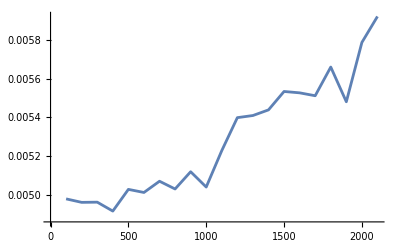
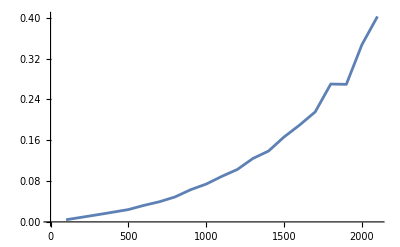
As predicted, with the relatively small chosen value for e, encryption is far faster than decryption.
We can also see that the encryption and decryption speeds as a function of key length ∈Ο(n^2)

Decryption:
-Graphics-

Encryption:
-Graphics-

## Code

### Task 1 : RSA

```mathematica
ClearAll["`*"]
```

#### functions

First we generate our keys; p,q,n,d,e.
we put this inside a function, this makes it easier later when we are benchmarking.

```mathematica
generateKeys[bits_] :=
Module[{},
p = RandomPrime[{2^(bits/2 -1),2^(bits/2)}];
q=RandomPrime[{2^(bits/2 -1),2^(bits/2)}];
n = p q;
ϕ = (p-1) (q-1);
rndInt := RandomInteger[{10^3,10^4}];
While[GCD[e=rndInt, ϕ]≠1];
d =PowerMod[e,-1,ϕ];
]
```

We put the encryption/decryption specific PowerMod calls into functions so we can easily map them over lists later.
We do the same with the encode/decode functions.

```mathematica
encrypt[x_] := PowerMod[x,e,n]
decrypt[x_] := PowerMod[x,d,n]

B=256;
encode[x_] := x. B^(Range[Length[x]]-1)
decode[0] := {}
decode[x_]:= Flatten[{Mod[x,B],decode[Quotient[x,B]]}]
```

These functions puts it all in a neat package, encodeEncrypt takes a string and outputs a cipher, decodeDecrypt takes a cipher and outputs a string.

```mathematica
encodeEncrypt[message_] :=
Module[{m,B},m=message;
m = Partition[ToCharacterCode[m],UpTo[20]];
m = Map[encode,m];
m=Map[encrypt,m]]

decodeDecrypt[crypt_] :=
Module[{d,B},d=crypt;
d = Map[decrypt,d];
d = Flatten[Map[decode, d]];
d = FromCharacterCode[d]]
```

#### Test

```mathematica
generateKeys[200];
```

```mathematica
message = "A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them.Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark.
asdfasdf";
```

```mathematica
crypt = encodeEncrypt[message];
decrypted = decodeDecrypt[crypt]
```

A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them.Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark.
asdfasdf

#### Benchmarks

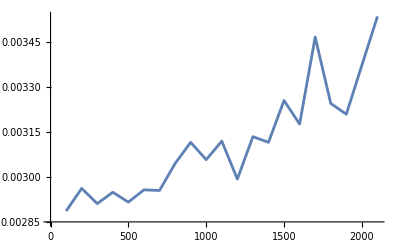

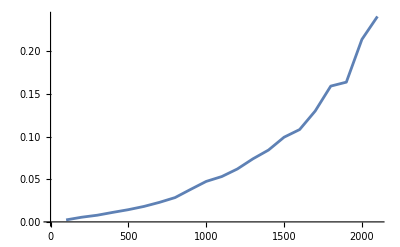

```mathematica
generateKeys[4096];
time[bits_]:=
Module[{s},s={1,2};
generateKeys[bits];
s[[1]] ={bits, Timing[crypt = encodeEncrypt[message];][[1]]};s[[2]]={bits, Timing[messageout =  decodeDecrypt[crypt];][[1]]};
s]
times =Map[time,Range[100,2100,100]];

ListPlot[{times[[All,1]]},{Joined -> True}]
ListPlot[{times[[All,2]]},{Joined -> True}]
```

### Task 2:

```mathematica
generateKeys[100];
cipher = encodeEncrypt[message];

RSAcrack[cipher_,n_,e_] :=
Module[{y},y=0;
y= FactorInteger[n]
]
FactorInteger[n]
```

{{644402813221553,1},{802921871735413,1}}